```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

NDSolve::ndsz: At z == 0.0005453009565735108481801647130136993014404376842113203276652949905225644202943721050930376429620566993, step size is effectively zero; singularity or stiff system suspected.

{9/10,0.0005259412266402355766917068495813500356173900860741903596742120124123937347486075047302715986632776335,0.4158378238756834717831719678876600008035515306794502454425522452785155827704796297791357622188943789,387.269766824327516716510218966183281864351480433919075489359774370285602221376230432713661460435,0.07566801314711718262635891885528107344425857793008}

NDSolve::ndsz: At z == 0.0005453009565735108481801647130136993014404376842113203276652949905225644202943721050930376429620566993, step size is effectively zero; singularity or stiff system suspected.

{9/10,0.0005453007582045347260355114584265053816651116201189500483157378415807919232108591481597437169509698141,0.4311445255928652117729805961820523206130070787049193969235579610530323266899163949016254966411964104,404.7583969563704405307156143542648325949323885333248448364830874421268120366728846570471424,0.0318579111513181787446110686639211005919201077675}

NDSolve::ndsz: At z == 0.0005453009565735108481801647130136993014404376842113203276652949905225644202943721050930376429620566993, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

{9/10,0.0005453009565713132593919174479356351491129152223189780168013206904095389810708293644405234234879017228,0.4311446824324612280135497634346980377860548842907615203339406498814433587860151092685080491622863671,365.36290888793155062003392925472820932519974575783474061742776071832775272696614340301,0.0154651907250567185443808163390672234683180268664}

{9/10,0.0005453009565735108238345535763570365604804588100355544440104701810352460126096670120223806261675808448,0.4311446824341987423390382323654633810602249442421967829295984962748409702391905970403999439112468574,329.799195317605668918818213568156901403395289191053232850309414155898243395884378,0.007507514892150268674832655757770365093833702744717}

{9/10,0.0005453009565735108481798950043289506524162079880677122444396110659518981773698260869318828540942781768,0.4311446824341987615877932036949545300583433395120823941568906895252183750741600283413887186566271694,297.69725951409753788001234364606432176595968255560272173099825807267055848518,0.003644492853039199999193682835268135011987776760832}

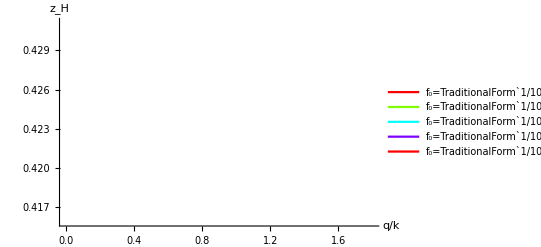

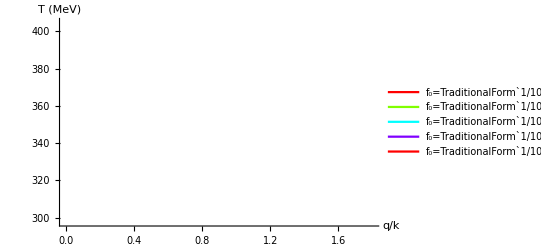

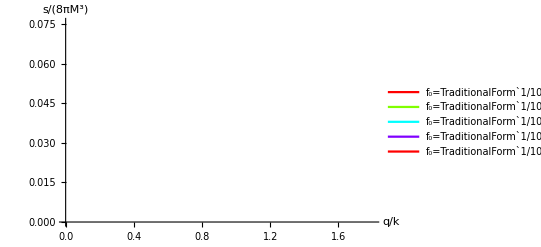

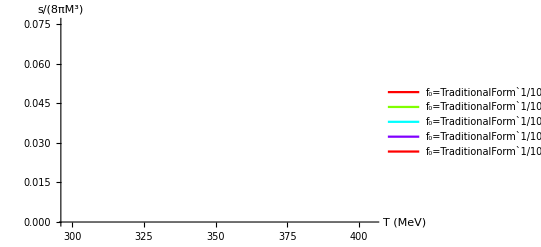

```mathematica
results={};
sols={};
(*δvec=(Table[10^eδ,{eδ,-20,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
f0vec=Table[10^eδ,{eδ,-20,-1}]//Reverse;*)
δvec={10^-1}//Reverse;
f0vec=Table[10^eδ,{eδ,-21,-1,5}]//Reverse;
For[if0=1,if0≤Length[f0vec],if0+=1,
fixf0results={};
f0=f0vec[[if0]];
For[iδ=1,iδ≤Length[δvec],iδ+=1,
δ=δvec[[iδ]];
ϵ=10^-40;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
(*dfdzAtϵ=-((4 (k-q) (9 k^2 (k-q)-6 ⅇ^(2/3 (1/k+ϵ)^2 λ) k (3 k^2+4 (1+k ϵ)^2 λ)+ⅇ^(4/3 (1/k+ϵ)^2 λ) ϵ (2+(k+q) ϵ) λ (9 k^2+4 (1+k ϵ)^2 λ)))/(36 k^2 (k-q)^2 ϵ-3 ⅇ^(2/3 (1/k+ϵ)^2 λ) k (k-q) (3 k (-1+8 k ϵ-q ϵ)+32 ϵ (1+k ϵ)^2 λ)+ⅇ^(4/3 (1/k+ϵ)^2 λ) (9 k^3 (-1+4 k ϵ-q ϵ)+12 k (-1+ϵ (-q+k (3+ϵ (8 k^2 ϵ+k (15-q ϵ)-q (8+3 q ϵ))))) λ+16 ϵ (1+2 k ϵ-q ϵ) (3+2 k ϵ+q ϵ) (λ+k ϵ λ)^2)));*)
(*//.{z->ϵ,ϕ[ϵ]->ic1[[2]],ϕ'[ϵ]->ic2[[2]],G[ϵ]->ic3[[2]],G'[ϵ]->ic4[[2]]}*)
(*Print[StringForm["Check: ``,``",1-δ,ϵ dfdzAtϵ//N]];*)
ic5=f[ϵ]==1+0ϵ dfdzAtϵ;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
fExact[z_]:=1;
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->100,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
sol=First[{ϕ,G,f,β}/.First[tmp]];
(*sol={ϕ,G,f,β}/.ParametricNDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,3/k},{q},AccuracyGoal->∞,WorkingPrecision->25,MaxSteps->∞];*)
{zmin,zmax}=First[sol[[1]]["Domain"]];
zH=tmp[[2,1,1]];
A[z_]:=NIntegrate[(sol[[4]][zp])/(q zp+1),{zp,ϵ,z},MaxRecursion->1000000,Method->{"GlobalAdaptive",MaxErrorIncreases->10000},WorkingPrecision->50];
coeff=Exp[-3A[zH]];
(*Print[StringForm["coeff=``",coeff]];*)
(*Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff}];*)
(*tmp=NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6,f[Rationalize[zH,0]]==f0},{ϕ,G,f,β},{z,ϵ,Rationalize[zH,0]}];
altsol={ϕ,G,f,β}/.First[tmp];
zHImproved=z/.FindRoot[altsol[[3]][z]==0,{z,zH},WorkingPrecision->25]//Quiet;
AppendTo[sols,altsol[[3]]];*)
AppendTo[sols,sol];
Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff}];
AppendTo[fixf0results,{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff}]];
AppendTo[results,fixf0results]]
(*Plot[{sol[[1]][z],(sol[[2]][z])^2/(6 √6)}//Evaluate,{z,ϵ,zHImproved}]*)
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
plotLegends=Table[StringForm["f_0=``",f0vec[[i]]],{i,Length[results]}];
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{4,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
```

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[sols]}]],{i,Length[sols]}];
plotLegends=Table[StringForm["q/k=``",results[[;;,;;,1]][[1,i]]],{i,Length[sols]}];
Show[Table[Plot[sols[[i]][[1]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["ϕ",16]}],{i,Length[sols]}],PlotRange->All];
Show[Table[Plot[sols[[i]][[2]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["G",16]}],{i,Length[sols]}],PlotRange->All];
Show[Table[Plot[sols[[i]][[3]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["f",16]}],{i,Length[sols]}],PlotRange->All];
Show[(Table[LogLogPlot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}]~Join~{LogLogPlot[2 x^-α/.{α->1(√553-23)/12},{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,-1]]-1},PlotStyle->Black,AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]}]}),PlotRange->All]
Show[(Table[LogLogPlot[sols[[i]][[2]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}]~Join~{LogLogPlot[6 x^-α/.{α->1(√553-23)/12},{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,-1]]-1},PlotStyle->Black,AxesLabel->{Style["ϵ=x_H-x",16],Style["G",16]}]}),PlotRange->All]
Show[(Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[1,i]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[1,i]]-1]},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}]~Join~{Plot[Log[(E^lnx)^1]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[1,-1]]-1]},PlotStyle->Black,AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100]}),PlotRange->All]
```

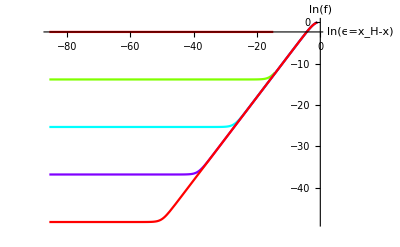

log_log_f_vs_ϵ_various_f0.pdf

```mathematica
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Export["log_log_f_vs_ϵ_various_f0.pdf",%]
```

```mathematica
DumpSave["/home/cplumber/AdSYMatFiniteT_Project/full/dump.mx","Global`"];
```

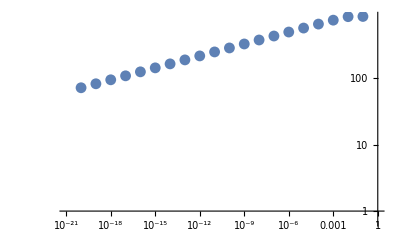

```mathematica
ListLogLogPlot[{f0vec,results[[;;,34,4]]}//Transpose,AxesOrigin->{0,0},PlotRange->{{10^-21,1},Automatic}]
```

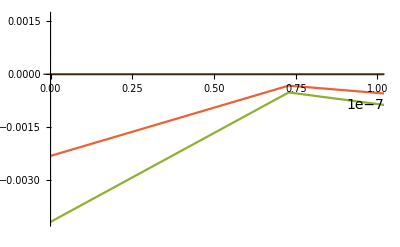

```mathematica
tmpPlot=Module[{ϕ,G,f,β},
ϕ[z_]:=altsol[[1]][z];
G[z_]:=altsol[[2]][z];
f[z_]:=altsol[[3]][z];
β[z_]:=altsol[[4]][z];
eqn1LHS=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2;
eqn1RHS=ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2LHS=6(a ϕ'[z]β[z]+β'[z]);
eqn2RHS=(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3LHS=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z];
eqn3RHS=1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4LHS=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z];
eqn4RHS=1/(q z+1)dςdG[ϕ[z],G[z]];
Plot[{2(eqn1LHS-eqn1RHS)/(eqn1LHS+eqn1RHS),2(eqn2LHS-eqn2RHS)/(eqn2LHS+eqn2RHS),2(eqn3LHS-eqn3RHS)/(eqn3LHS+eqn3RHS),2(eqn4LHS-eqn4RHS)/(eqn4LHS+eqn4RHS)}//Evaluate,{z,ϵ,zH},PlotRange->{{0,10^-7},All}]];
tmpPlot
```

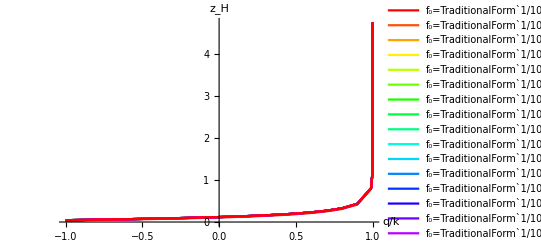

zH_vs_qByk.pdf

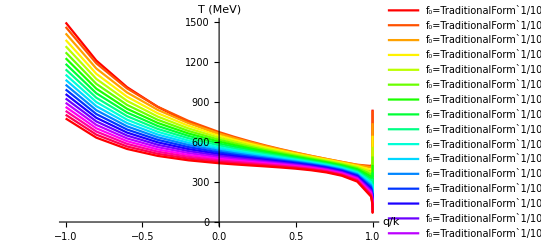

TH_vs_qByk.pdf

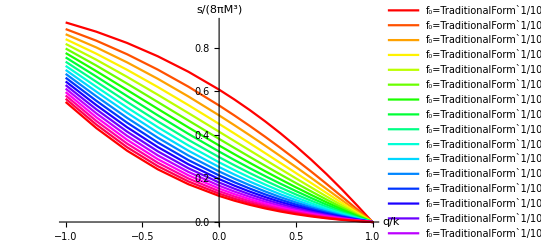

s_vs_qByk.pdf

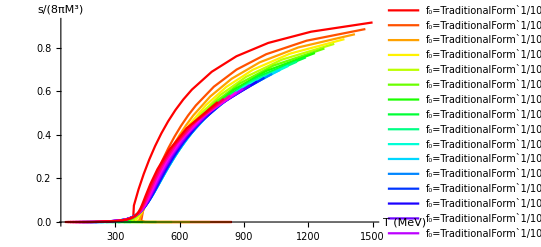

s_vs_T_from_qByk.pdf

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
plotLegends=Table[StringForm["f_0=``",f0vec[[i]]],{i,Length[results]}];
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["zH_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["TH_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["s_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{4,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["s_vs_T_from_qByk.pdf",%]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
dΩdϕ[ϕ_,G_]:=(-a+a ⅇ^(-a ϕ)) k;
dΩdG[ϕ_,G_]:=k U'[G];
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+dΩdϕ[ϕ,G])^2+(dΩdG[ϕ,G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
ϕ[z_]:=G[z]^2/(6 √6);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
eqn1//FullSimplify
eqn2//FullSimplify
eqn3//FullSimplify
eqn4//FullSimplify
```

1/36 k^2 (432+30 G[z]^2+G[z]^4)+3 (1+q z) (β[z] (f'[z]+1/18 f[z] G[z] G'[z])+f[z] β'[z])==12 f[z] β[z]^2

G'[z] (-18 G[z] β[z]+(1+q z) (54+G[z]^2) G'[z])==324 β'[z]

1/(1+q z)(3 k^2 G[z]^4+18 (1+q z)^2 f[z] G'[z]^2+G[z]^2 (36 k^2+(1+q z)^2 f[z] G'[z]^2)+18 (1+q z) G[z] ((f[z] (q-4 β[z])+(1+q z) f'[z]) G'[z]+(1+q z) f[z] G''[z]))==0

(k^2 G[z] (18+G[z]^2))/(6+6 q z)+(1+q z) f'[z] G'[z]+f[z] ((q-4 β[z]) G'[z]+1/18 (1+q z) G[z] G'[z]^2+(1+q z) G''[z])==0